```mathematica
minTimeResolutionMS = 20
```

20

```mathematica
windowOverlapMS = 10
```

10

```mathematica
channel = 1
```

1

```mathematica
utt135 =Import["~/workspace/gnu-radio/recordings/1_3_5.wav"]
```

-Graphics-

```mathematica
utt354 =Import["~/workspace/gnu-radio/recordings/3_5_4.wav"]
```

-Graphics-

#### Formula to determine the number of samples required from a given wav file to stretch a given time window

```mathematica
SamplesPerWindow[wav_, windowSizeMS_] := (windowSizeMS/((Length[wav[[1,1,channel]]]/wav[[1,2]])*1000))*Length[wav[[1,1,1]]]
```

```mathematica
uttSampleWindowSize = SamplesPerWindow[utt135, minTimeResolutionMS]
```

882

```mathematica
HammingWindow[0]
```

1

```mathematica
windowStartInterval = uttSampleWindowSize-SamplesPerWindow[utt135,windowOverlapMS]
```

441

```mathematica
HammingVector = Table[
HammingWindow[0.5*((i-windowStartInterval)/windowStartInterval)],{i,0,uttSampleWindowSize}]
```

{0.0869565,0.0869681,0.0870029,0.0870608,0.0871419,0.0872461,871,0.0872461,0.0871419,0.0870608,0.0870029,0.0869681,0.0869565}
 |  |  |  |

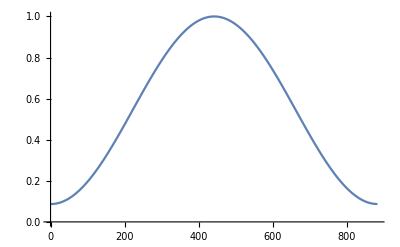

```mathematica
ListLinePlot[HammingVector]
```

```mathematica
TotalNumberOfWindows = Floor[Length[utt135[[1,1,channel]]]/windowStartInterval]
```

500

```mathematica
partitionedData = Partition[utt135[[1,1,1]], Length[HammingVector], windowStartInterval]
```

{1}
 |  |  |  |

```mathematica
theWindows=Map[HammingVector #&, partitionedData]
```

{{0.00110925,0.0000902379,0.000249581,0.000268345,-0.000103715,873,0.000585059,0.00123279,0.00125056,0.000737828,0.00114905},496,{1}}
 |  |  |  |

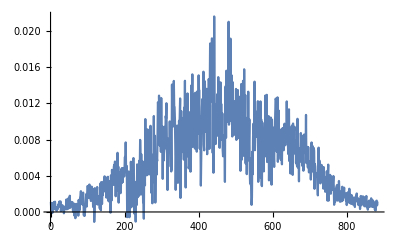

```mathematica
ListLinePlot[theWindows[[1]]]
```

```mathematica
ListLinePlot[Abs[Fourier[theWindows[[1]]]]]
```

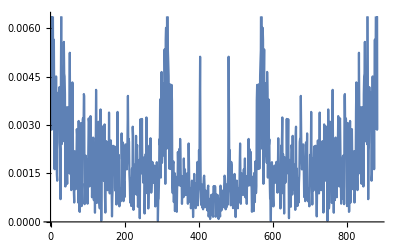

```mathematica
theWindowDfts = Fourier
```

```mathematica
filtered = BandpassFilter[Abs[Fourier[theWindows[[1]]]], {.1,1.00}]
```

{0.0930943,0.0522011,0.0128802,-0.011234,-0.0167272,-0.0105837,871,-0.000843794,-0.00430674,-0.00493072,0.00173805,0.0167263,0.0356458}
 |  |  |  |

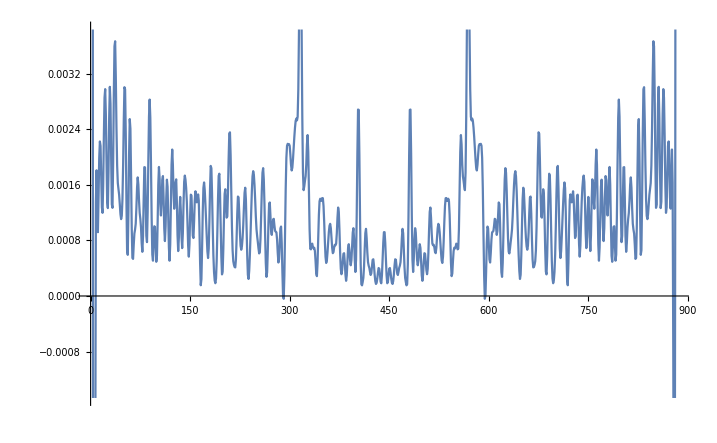

```mathematica
ListLinePlot[filtered]
```

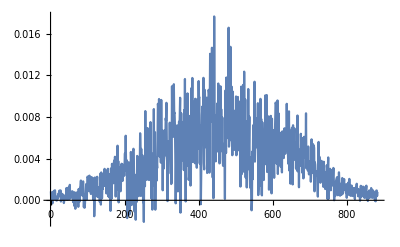

```mathematica
ListLinePlot[BandpassFilter[theWindows[[1]], {.1, 10}]]
```

```mathematica
enc = Aud["AudioMFCC"]
```

NetEncoder[AudioMFCC]

```mathematica
enc[theWindows[[1]]]
```

NetEncoder[AudioMFCC][{0.00110925,0.0000902379,0.000249581,0.000268345,-0.000103715,873,0.000585059,0.00123279,0.00125056,0.000737828,0.00114905}]
 |  |  |  |